# Simulation

## Pre-function

## Basic Function

```mathematica
SpinEigenstate={{1,0},{0,1}};PhononEigenstate[n_]:=Module[{circle},circle=Table[i,{i,1,n+1}];Table[Nest[Permute[#,Cycles[{circle}]]&,{Table[0,{i,1,n}],1}//Flatten,j],{j,1,n+1}]];
```

```mathematica
DensityMatrix[State_]:=Outer[Times,Conjugate@State,State]/(Conjugate@State.State)
```

```mathematica
ReducedSpinDensityMatrix[State_,PhononNumber_]:=Module[{wholeDensityMatrix},wholeDensityMatrix=DensityMatrix[State];Table[Sum[(Normalize@Flatten[KroneckerProduct[Nest[Permute[#,Cycles[{{1,2,3,4}}]]&,{0,0,0,1},i],PhononEigenstate[PhononNumber][[p]]]]).wholeDensityMatrix.(Normalize@Flatten@KroneckerProduct[Nest[Permute[#,Cycles[{{1,2,3,4}}]]&,{0,0,0,1},j],PhononEigenstate[PhononNumber][[p]]]),{p,1,PhononNumber+1}]//Chop,{i,1,4},{j,1,4}]]
```

```mathematica
PopulationSingleParticle[M_,g_,PhononNumber_]:=Sum[(Normalize@Flatten[KroneckerProduct[Nest[Permute[#,Cycles[{{1,2}}]]&,{0,1},g],PhononEigenstate[PhononNumber][[p]]]]).M.(Normalize@Flatten@KroneckerProduct[Nest[Permute[#,Cycles[{{1,2}}]]&,{0,1},g],PhononEigenstate[PhononNumber][[p]]]),{p,1,PhononNumber+1}]//Chop
```

```mathematica
Population[M_,g_,PhononNumber_]:=Sum[(Normalize@Flatten[KroneckerProduct[Nest[Permute[#,Cycles[{{1,2,3,4}}]]&,{0,0,0,1},g],PhononEigenstate[PhononNumber][[p]]]]).M.(Normalize@Flatten@KroneckerProduct[Nest[Permute[#,Cycles[{{1,2,3,4}}]]&,{0,0,0,1},g],PhononEigenstate[PhononNumber][[p]]]),{p,1,PhononNumber+1}]//Chop
```

```mathematica
PhononDistribution[M_,g_,PhononNumber_]:=Sum[(Normalize@Flatten[KroneckerProduct[Nest[Permute[#,Cycles[{{1,2,3,4}}]]&,{0,0,0,1},p],PhononEigenstate[PhononNumber][[g]]]]).M.(Normalize@Flatten@KroneckerProduct[Nest[Permute[#,Cycles[{{1,2,3,4}}]]&,{0,0,0,1},p],PhononEigenstate[PhononNumber][[g]]]),{p,1,4}]//Chop
```

```mathematica
UParity[ϕ_,θ_]=({{Cos[θ/2], -I E^(I ϕ)Sin[θ/2]}, {-I E^(-I ϕ)Sin[θ/2], Cos[θ/2]}})
```

{{Cos[θ/2],-ⅈ ⅇ^(ⅈ ϕ) Sin[θ/2]},{-ⅈ ⅇ^(-ⅈ ϕ) Sin[θ/2],Cos[θ/2]}}

```mathematica
UParityTwoIon[ϕ_,θ1_,θ2_]=KroneckerProduct[UParity[ϕ,θ1],UParity[ϕ,θ2]]
```

{{Cos[θ1/2] Cos[θ2/2],-ⅈ ⅇ^(ⅈ ϕ) Cos[θ1/2] Sin[θ2/2],-ⅈ ⅇ^(ⅈ ϕ) Cos[θ2/2] Sin[θ1/2],-ⅇ^(2 ⅈ ϕ) Sin[θ1/2] Sin[θ2/2]},{-ⅈ ⅇ^(-ⅈ ϕ) Cos[θ1/2] Sin[θ2/2],Cos[θ1/2] Cos[θ2/2],-Sin[θ1/2] Sin[θ2/2],-ⅈ ⅇ^(ⅈ ϕ) Cos[θ2/2] Sin[θ1/2]},{-ⅈ ⅇ^(-ⅈ ϕ) Cos[θ2/2] Sin[θ1/2],-Sin[θ1/2] Sin[θ2/2],Cos[θ1/2] Cos[θ2/2],-ⅈ ⅇ^(ⅈ ϕ) Cos[θ1/2] Sin[θ2/2]},{-ⅇ^(-2 ⅈ ϕ) Sin[θ1/2] Sin[θ2/2],-ⅈ ⅇ^(-ⅈ ϕ) Cos[θ2/2] Sin[θ1/2],-ⅈ ⅇ^(-ⅈ ϕ) Cos[θ1/2] Sin[θ2/2],Cos[θ1/2] Cos[θ2/2]}}

```mathematica
AnalyticParityEvolve[ρ_,θ1_,θ2_]:=Module[{ρAfterParity},ρAfterParity=Refine[ComplexExpand@(UParityTwoIon[ϕ,θ1,θ2].ρ.UParityTwoIon[ϕ,θ1,θ2]†),ϕ∈Reals]//Chop//FullSimplify;Plot[ρAfterParity[[1,1]]+ρAfterParity[[4,4]]-ρAfterParity[[2,2]]-ρAfterParity[[3,3]],{ϕ,0,2π}]]
```

## Basic Matrixs

```mathematica
MaxPhononNumber=4;
```

```mathematica
Id={{1,0},{0,1}};
Px={{0,1},{1,0}};
Py={{0,-ⅈ},{ⅈ,0}};
Pz={{1,0},{0,-1}};
Pm={{0,1},{0,0}};
Pp={{0,0},{1,0}};
σx[j_]:=KroneckerProduct[IdentityMatrix[ 2^(NumofIons-j)],KroneckerProduct[Px,IdentityMatrix[ 2^(j-1)]]]
σy[j_]:=KroneckerProduct[IdentityMatrix[ 2^(NumofIons-j)],KroneckerProduct[Py,IdentityMatrix[ 2^(j-1)]]]
σz[j_]:=KroneckerProduct[IdentityMatrix[ 2^(NumofIons-j)],KroneckerProduct[Pz,IdentityMatrix[ 2^(j-1)]]]
σp[j_]:=KroneckerProduct[IdentityMatrix[ 2^(NumofIons-j)],KroneckerProduct[Pp,IdentityMatrix[ 2^(j-1)]]]
σm[j_]:=KroneckerProduct[IdentityMatrix[ 2^(NumofIons-j)],KroneckerProduct[Pm,IdentityMatrix[ 2^(j-1)]]]
```

```mathematica
Subscript[σ, x]=({{0, 1}, {1, 0}});Subscript[σ, z]=({{1, 0}, {0, -1}});Subscript[σ, y]=({{0, -I}, {I, 0}});SubPlus[σ]=({{0, 1}, {0, 0}});SubMinus[σ]=({{0, 0}, {1, 0}});a=KroneckerProduct[IdentityMatrix[2],IdentityMatrix[2],Table[KroneckerDelta[i,j-1] √j,{i,0,MaxPhononNumber},{j,0,MaxPhononNumber}]];adag=KroneckerProduct[IdentityMatrix[2],IdentityMatrix[2],Table[KroneckerDelta[i,j+1] √(j+1),{i,0,MaxPhononNumber},{j,0,MaxPhononNumber}]];
```

```mathematica
SpinRotation[θ_,φ_]:=MatrixExp[KroneckerProduct[-ⅈ θ/2((∑_(k=1)^NumofIons σx[k])Cos[φ]+(∑_(k=1)^NumofIons σy[k])Sin[φ]),IdentityMatrix[MaxPhononNumber+1]]]
```

```mathematica
σZ[i_]:=KroneckerProduct@@Flatten[{Nest[Permute[#,Cycles[{{1,2}}]]&,{IdentityMatrix[2],Subscript[σ, z]},i],{IdentityMatrix[MaxPhononNumber+1]}},1]
```

```mathematica
σP[i_]:=KroneckerProduct@@Flatten[{Nest[Permute[#,Cycles[{{1,2}}]]&,{IdentityMatrix[2],SubPlus[σ]},i],{IdentityMatrix[MaxPhononNumber+1]}},1]
```

```mathematica
σM[i_]:=KroneckerProduct@@Flatten[{Nest[Permute[#,Cycles[{{1,2}}]]&,{IdentityMatrix[2],SubMinus[σ]},i],{IdentityMatrix[MaxPhononNumber+1]}},1]
```

```mathematica
pnt=800;TwoIonSimulation[Ω_,δ_,ν_,MaxPhononNumber_,SimulationTime_,only_,initialState_: Normalize[KroneckerProduct[{0,1},{0,1},{1,Table[0,{i,1,MaxPhononNumber}]}//Flatten]//Flatten],Hamcar_:0,export_:False,plotTrue_:True]:=Module[{IHamiltonian,a,adag,σZ,σP,σM,sol,data,Hambsb,Hamrsb,δωb,δωr,end},δωb=2π δ[[1]];δωr=2π δ[[2]];a=KroneckerProduct[IdentityMatrix[2],IdentityMatrix[2],Table[KroneckerDelta[i,j-1] √j,{i,0,MaxPhononNumber},{j,0,MaxPhononNumber}]];adag=KroneckerProduct[IdentityMatrix[2],IdentityMatrix[2],Table[KroneckerDelta[i,j+1] √(j+1),{i,0,MaxPhononNumber},{j,0,MaxPhononNumber}]];σZ[i_]:=KroneckerProduct@@Flatten[{Nest[Permute[#,Cycles[{{1,2}}]]&,{IdentityMatrix[2],Subscript[σ, z]},i],{IdentityMatrix[MaxPhononNumber+1]}},1];σP[i_]:=KroneckerProduct@@Flatten[{Nest[Permute[#,Cycles[{{1,2}}]]&,{IdentityMatrix[2],SubPlus[σ]},i],{IdentityMatrix[MaxPhononNumber+1]}},1];σM[i_]:=KroneckerProduct@@Flatten[{Nest[Permute[#,Cycles[{{1,2}}]]&,{IdentityMatrix[2],SubMinus[σ]},i],{IdentityMatrix[MaxPhononNumber+1]}},1];Hambsb=∑_(ni=1)^2 2π Ω[[1,ni]]σP[ni].(-ⅈ η (a ⅇ^(-ⅈ 2π ν t)+adag ⅇ^(ⅈ 2π ν t) )+IdentityMatrix[4*(MaxPhononNumber+1)])*ⅇ^(ⅈ δωb  t)+∑_(ni=1)^2 2π Ω[[2,ni]]σM[ni].(ⅈ (η a ⅇ^(-ⅈ 2π ν t)+η a† ⅇ^(ⅈ 2π ν t) )+IdentityMatrix[4*(MaxPhononNumber+1)])*ⅇ^(-ⅈ δωb  t)//Chop//Simplify;Hamrsb=∑_(ni=1)^2 2π Ω[[3,ni]]σP[ni].(-ⅈ η (a ⅇ^(-ⅈ 2π ν t)+a† ⅇ^(ⅈ 2π ν t) )+IdentityMatrix[4*(MaxPhononNumber+1)])*ⅇ^(ⅈ δωr  t)+∑_(ni=1)^2 2π Ω[[4,ni]]σM[ni].(ⅈ η ( a ⅇ^(-ⅈ 2π ν t)+adag ⅇ^(ⅈ 2π ν t) )+IdentityMatrix[4*(MaxPhononNumber+1)])*ⅇ^(-ⅈ δωr  t)//Chop//Simplify;IHamiltonian=Hambsb+Hamrsb+Hamcar;sol=NDSolve[{I D[c[t],t]==(IHamiltonian).c[t],c[0]==initialState},c,{t,0,SimulationTime},MaxSteps->Infinity];If[export,expoteSolution=sol];If[plotTrue==False,Goto[end]];If[only=="Individual",data=Table[{t,Population[DensityMatrix[Evaluate[c[t]/.sol[[1]]]],i,MaxPhononNumber]},{i,1,4},{t,0,SimulationTime,SimulationTime/pnt}];Print[ListLinePlot[data,PlotStyle->({Thick,#}&/@{Blue,Green,Yellow,Red}),PlotLegends->{"11","10","01","00"},Frame->True,PlotRange->All]],data=Table[{t,2Population[DensityMatrix[Evaluate[c[t]/.sol[[1]]]],1,MaxPhononNumber]+Population[DensityMatrix[Evaluate[c[t]/.sol[[1]]]],2,MaxPhononNumber]+Population[DensityMatrix[Evaluate[c[t]/.sol[[1]]]],3,MaxPhononNumber]},{t,0,SimulationTime,SimulationTime/pnt}];Print[ListLinePlot[data,Frame->True,PlotStyle->Blue]]];Label[end];]
```

```mathematica
TwoIonSimulationTwoModes[Ω_,δ_,ν_,MaxPhononNumber_,SimulationTime_,only_,initialState_: Normalize[KroneckerProduct[{0,1},{0,1},{1,Table[0,{i,1,MaxPhononNumber}]}//Flatten]//Flatten],Hamcar_:0,export_:False]:=Module[{IHamiltonian,a,adag,σZ,σP,σM,sol,data,Hambsb,Hamrsb,δωb,δωr,end},δωb=2π δ[[1]];δωr=2π δ[[2]];a=KroneckerProduct[IdentityMatrix[2],IdentityMatrix[2],Table[KroneckerDelta[i,j-1] √j,{i,0,MaxPhononNumber},{j,0,MaxPhononNumber}]];adag=KroneckerProduct[IdentityMatrix[2],IdentityMatrix[2],Table[KroneckerDelta[i,j+1] √(j+1),{i,0,MaxPhononNumber},{j,0,MaxPhononNumber}]];σZ[i_]:=KroneckerProduct@@Flatten[{Nest[Permute[#,Cycles[{{1,2}}]]&,{IdentityMatrix[2],Subscript[σ, z]},i],{IdentityMatrix[MaxPhononNumber+1]}},1];σP[i_]:=KroneckerProduct@@Flatten[{Nest[Permute[#,Cycles[{{1,2}}]]&,{IdentityMatrix[2],SubPlus[σ]},i],{IdentityMatrix[MaxPhononNumber+1]}},1];σM[i_]:=KroneckerProduct@@Flatten[{Nest[Permute[#,Cycles[{{1,2}}]]&,{IdentityMatrix[2],SubMinus[σ]},i],{IdentityMatrix[MaxPhononNumber+1]}},1];Hambsb=∑_(ni=1)^2 2π Ω[[1,ni]]σP[ni].(-ⅈ η (a ⅇ^(-ⅈ 2π ν t)+adag ⅇ^(ⅈ 2π ν t) )+IdentityMatrix[4*(MaxPhononNumber+1)])*ⅇ^(ⅈ δωb  t)+∑_(ni=1)^2 2π Ω[[2,ni]]σM[ni].(ⅈ (η a ⅇ^(-ⅈ 2π ν t)+η a† ⅇ^(ⅈ 2π ν t) )+IdentityMatrix[4*(MaxPhononNumber+1)])*ⅇ^(-ⅈ δωb  t)//Chop//Simplify;Hamrsb=∑_(ni=1)^2 2π Ω[[3,ni]]σP[ni].(-ⅈ η (a ⅇ^(-ⅈ 2π ν t)+a† ⅇ^(ⅈ 2π ν t) )+IdentityMatrix[4*(MaxPhononNumber+1)])*ⅇ^(ⅈ δωr  t)+∑_(ni=1)^2 2π Ω[[4,ni]]σM[ni].(ⅈ η ( a ⅇ^(-ⅈ 2π ν t)+adag ⅇ^(ⅈ 2π ν t) )+IdentityMatrix[4*(MaxPhononNumber+1)])*ⅇ^(-ⅈ δωr  t)//Chop//Simplify;IHamiltonian=Hambsb+Hamrsb+Hamcar;sol=NDSolve[{I D[c[t],t]==(IHamiltonian).c[t],c[0]==initialState},c,{t,0,SimulationTime},MaxSteps->Infinity];If[export,expoteSolution=1];If[only=="Individual",data=Table[{t,Population[DensityMatrix[Evaluate[c[t]/.sol[[1]]]],i,MaxPhononNumber]},{i,1,4},{t,0,SimulationTime,SimulationTime/pnt}];ListLinePlot[data,PlotStyle->({Thick,#}&/@{Blue,Green,Yellow,Red}),PlotLegends->{"11","10","01","00"},Frame->True],data=Table[{t,2Population[DensityMatrix[Evaluate[c[t]/.sol[[1]]]],1,MaxPhononNumber]+Population[DensityMatrix[Evaluate[c[t]/.sol[[1]]]],2,MaxPhononNumber]+Population[DensityMatrix[Evaluate[c[t]/.sol[[1]]]],3,MaxPhononNumber]},{t,0,SimulationTime,SimulationTime/pnt}];ListLinePlot[data,Frame->True,PlotStyle->Blue]]]
```

## Simulate the carrier and sideband

### Carrier simulation

#### Single ion carrier

```mathematica
Ω={{1/(4*4.5),0},{1/(4*4.5),0},{0,0},{0,0}};δ={0,0};ω={ωIon-0.9ν,ωIon+0.9ν};ν=1;ωIon=10;η=0.1;SimulationTime=20;
```

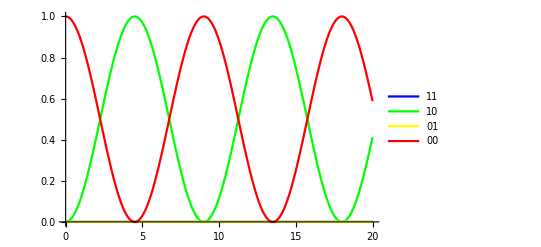

```mathematica
TwoIonSimulation[Ω,δ,ν,MaxPhononNumber,SimulationTime,"Individual"]
```

#### Two ion carrier

```mathematica
Ω={{1/(4*4.5),1/(4*4.0)},{1/(4*4.5),1/(4*4.0)},{0,0},{0,0}};δ={0,0};ω={ωIon-0.9ν,ωIon+0.9ν};ν=1;ωIon=10;η=0.1;SimulationTime=100;
```

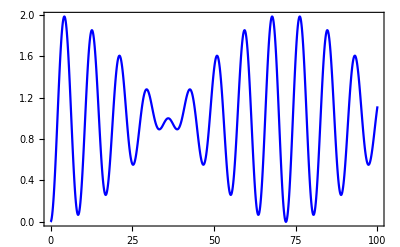

```mathematica
SimulationTime=100;TwoIonSimulation[Ω,δ,ν,MaxPhononNumber,SimulationTime,"Total"]
```

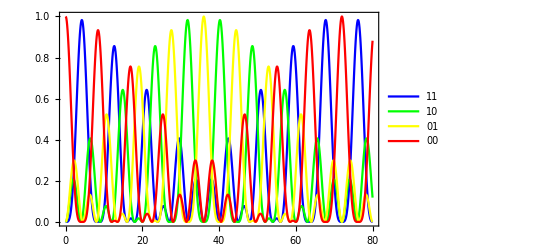

```mathematica
SimulationTime=80;TwoIonSimulation[Ω,δ,ν,MaxPhononNumber,SimulationTime,"Individual"]
```

### Blue sideband simulation

#### Single ion blue

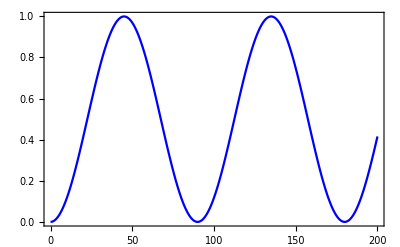

```mathematica
Ω={{1/(4*4.5),0},{1/(4*4.5),0},{0,0},{0,0}};δ={-ν,0};ω={ωIon-0.9ν,ωIon+0.9ν};ν=20;ωIon=10;η=0.1;SimulationTime=200;TwoIonSimulation[Ω,δ,ν,MaxPhononNumber,SimulationTime,"Total"]
```

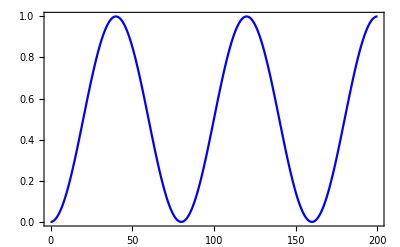

```mathematica
Ω={{0,1/(4*4.0)},{0,1/(4*4.0)},{0,0},{0,0}};δ={-ν,0};ω={ωIon-0.9ν,ωIon+0.9ν};ν=20;ωIon=10;η=0.1;SimulationTime=200;TwoIonSimulation[Ω,δ,ν,MaxPhononNumber,SimulationTime,"Total"]
```

#### Two ion blue

```mathematica
Ω={{1/(4*4.5),1/(4*4.0)},{1/(4*4.5),1/(4*4.0)},{0,0},{0,0}};δ={-ν,0};ω={ωIon-0.9ν,ωIon+0.9ν};ν=20;ωIon=10;η=0.1;SimulationTime=200;
```

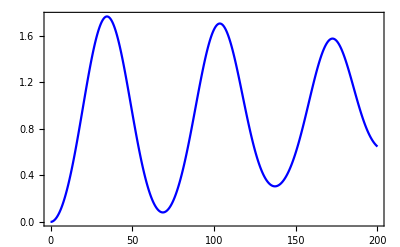

```mathematica
TwoIonSimulation[Ω,δ,ν,MaxPhononNumber,SimulationTime,"Total",True]
```

```mathematica
MaximalBy[expoteddata,#[[2]]&][[1]]
```

{69/2,1.76764}

## How phase effect the evolution

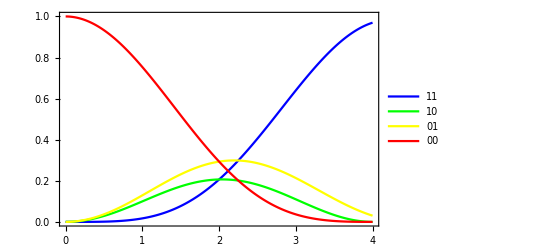

{c→InterpolatingFunction[{{0., 4.}}, <>]}

```mathematica
Ω={{1/(4*4.5),1/(4*4.0)},{1/(4*4.5),1/(4*4.0)},{0,0},{0,0}};δ={0,0};ω={ωIon-0.9ν,ωIon+0.9ν};ν=1.5;ωIon=10;η=0.1;SimulationTime=4;TwoIonSimulation[Ω,δ,ν,MaxPhononNumber,SimulationTime,"Individual",Normalize[KroneckerProduct[{0,1},{0,1},{1,Table[0,{i,1,MaxPhononNumber}]}//Flatten]//Flatten],0,True];FirstRotation=expoteSolution[[1]]
```

### Set the phase being π and we should drive the ion back original point.

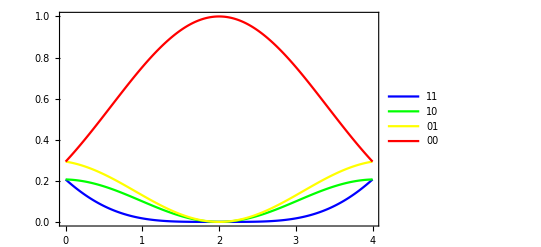

```mathematica
Ω={{1/(4*4.5),1/(4*4.0)},{1/(4*4.5),1/(4*4.0)},{0,0},{0,0}};δ={1/(2t),0};ω={ωIon-0.9ν,ωIon+0.9ν};ν=1.5;ωIon=10;η=0.1;SimulationTime=4;TwoIonSimulation[Ω,δ,ν,MaxPhononNumber,SimulationTime,"Individual",Evaluate@(c[2]/.FirstRotation),0,True];
```

```mathematica
Ω={{1/(4*4.5),1/(4*4.0)},{1/(4*4.5),1/(4*4.0)},{0,0},{0,0}};δ={1/(2t),0};ω={ωIon-0.9ν,ωIon+0.9ν};ν=1.5;ωIon=10;η=0.1;SimulationTime=4;TwoIonSimulation[Ω,δ,ν,MaxPhononNumber,SimulationTime,"Individual",Evaluate@(c[2]/.FirstRotation),0,True];
```

### Scan the phase

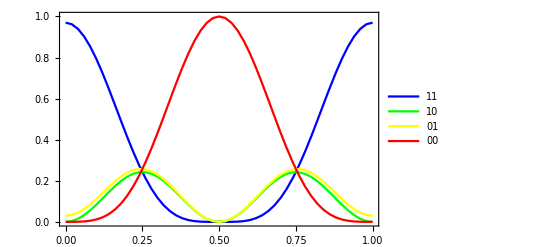

```mathematica
PhaseScan=Table[Ω={{1/(4*4.5),1/(4*4.0)},{1/(4*4.5),1/(4*4.0)},{0,0},{0,0}};δ={phi/t,0};ω={ωIon-0.9ν,ωIon+0.9ν};ν=1.5;ωIon=10;η=0.1;SimulationTime=5;TwoIonSimulation[Ω,δ,ν,MaxPhononNumber,SimulationTime,"Individual",Evaluate@(c[2]/.FirstRotation),0,True,False];{phi,Population[DensityMatrix[Evaluate[c[2]/.expoteSolution[[1]]]],i,MaxPhononNumber]},{i,1,4},{phi,0,1,1/50}];Show[ListLinePlot[#,PlotStyle->({Thick,#}&/@{Blue,Green,Yellow,Red}),PlotLegends->{"11","10","01","00"},Frame->True]]&@PhaseScan
```

## MS gate simulation

## Wrong setting

### Sideband position is not correct

If 11 cannot reach 1, means the detuning between RSB and BSB is not equal, which means we need to add a compensating term on one of the sideband frequency to make the 11 reach 1.

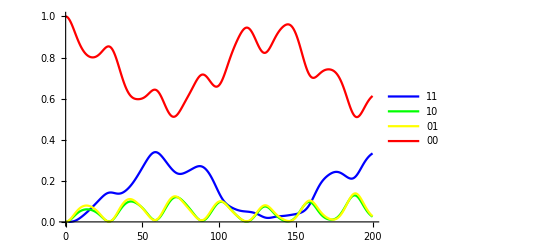

```mathematica
Ω={{1/(4*4.5),1/(4*4.0)},{1/(4*4.5),1/(4*4.0)},{1/(4*4.5),1/(4*4.0)},{1/(4*4.5),1/(4*4.0)}};δ={-ν+1/34+1/150,ν-1/34};ω={ωIon-0.9ν,ωIon+0.9ν};ν=20;ωIon=10;η=0.1;SimulationTime=200;
TwoIonSimulation[Ω,δ,ν,MaxPhononNumber,SimulationTime,"Individual"]
```

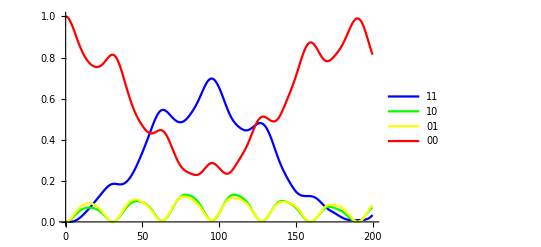

```mathematica
Ω={{1/(4*4.5),1/(4*4.0)},{1/(4*4.5),1/(4*4.0)},{1/(4*4.5),1/(4*4.0)},{1/(4*4.5),1/(4*4.0)}};δ={-ν+1/34+1/300,ν-1/34};ω={ωIon-0.9ν,ωIon+0.9ν};ν=20;ωIon=10;η=0.1;SimulationTime=200;
TwoIonSimulation[Ω,δ,ν,MaxPhononNumber,SimulationTime,"Individual"]
```

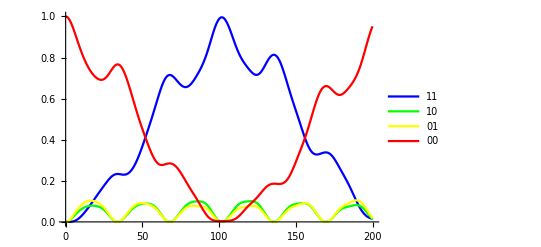

```mathematica
Ω={{1/(4*4.5),1/(4*4.0)},{1/(4*4.5),1/(4*4.0)},{1/(4*4.5),1/(4*4.0)},{1/(4*4.5),1/(4*4.0)}};δ={-ν+1/34,ν-1/34};ω={ωIon-0.9ν,ωIon+0.9ν};ν=20;ωIon=10;η=0.1;SimulationTime=200;
TwoIonSimulation[Ω,δ,ν,MaxPhononNumber,SimulationTime,"Individual"]
```

### Detuning is not correct

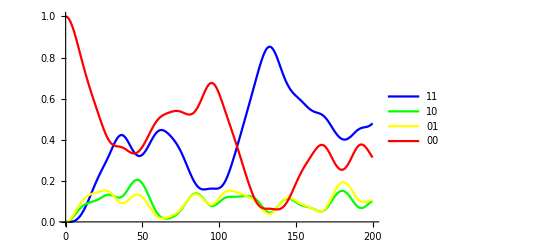

```mathematica
Ω={{1/(4*4.5),1/(4*4.0)},{1/(4*4.5),1/(4*4.0)},{1/(4*4.5),1/(4*4.0)},{1/(4*4.5),1/(4*4.0)}};δ={-ν+1/80,ν-1/80};ω={ωIon-0.9ν,ωIon+0.9ν};ν=20;ωIon=10;η=0.1;SimulationTime=200;TwoIonSimulation[Ω,δ,ν,MaxPhononNumber,SimulationTime,"Individual"]
```

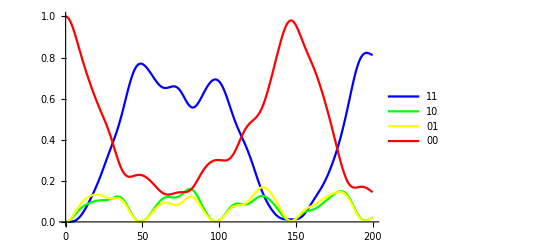

```mathematica
Ω={{1/(4*4.5),1/(4*4.0)},{1/(4*4.5),1/(4*4.0)},{1/(4*4.5),1/(4*4.0)},{1/(4*4.5),1/(4*4.0)}};δ={-ν+1/50,ν-1/50};ω={ωIon-0.9ν,ωIon+0.9ν};ν=20;ωIon=10;η=0.1;SimulationTime=200;TwoIonSimulation[Ω,δ,ν,MaxPhononNumber,SimulationTime,"Individual"]
```

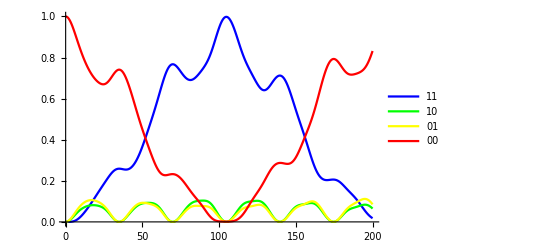

```mathematica
Ω={{1/(4*4.5),1/(4*4.0)},{1/(4*4.5),1/(4*4.0)},{1/(4*4.5),1/(4*4.0)},{1/(4*4.5),1/(4*4.0)}};δ={-ν+1/35,ν-1/35};ω={ωIon-0.9ν,ωIon+0.9ν};ν=20;ωIon=10;η=0.1;SimulationTime=200;TwoIonSimulation[Ω,δ,ν,MaxPhononNumber,SimulationTime,"Individual"]
```

### Correct setting

```mathematica
√(40*45.)
```

42.4264

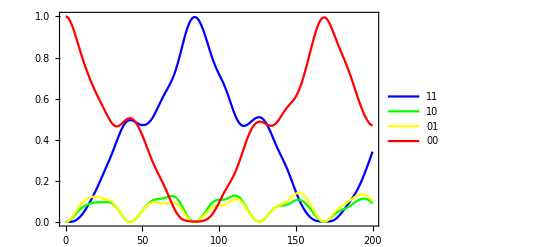

```mathematica
Ω={{1/(4*4.5),1/(4*4.0)},{1/(4*4.5),1/(4*4.0)},{1/(4*4.5),1/(4*4.0)},{1/(4*4.5),1/(4*4.0)}};δ={-ν+1/√(40*45),ν-1/√(40*45)+2/t};ω={ωIon-0.9ν,ωIon+0.9ν};ν=20;ωIon=10;η=0.1;SimulationTime=200;
TwoIonSimulation[Ω,δ,ν,MaxPhononNumber,SimulationTime,"Individual"]
```

Measure the parity (simulate the continuous evolution)

Note that the δ in at here are the frequency, not the angular frequency. The 2π phase corresponding 1/t at here.

## Example 1

```mathematica
Ω1=1/(4*4.482015445737576);Ω2=1/(4*4.0466432386367615);
```

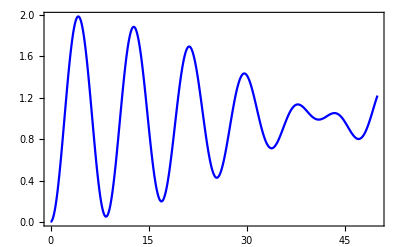

```mathematica
Ω={{Ω1,Ω2},{Ω1,Ω2},{0,0},{0,0}};δ={0,0};ω={ωIon-0.9ν,ωIon+0.9ν};ν=1;ωIon=10;η=0.1;SimulationTime=50;TwoIonSimulation[Ω,δ,ν,MaxPhononNumber,SimulationTime,"Total"]
```

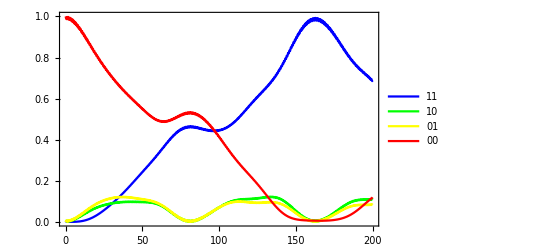

{c→InterpolatingFunction[{{0., 200.}}, <>]}

```mathematica
Ω={{Ω1,Ω2},{Ω1,Ω2},{Ω1,Ω2},{Ω1,Ω2}};ν=1.45;δ={-ν+1/82,ν-1/82};ωIon=10;η=0.051;SimulationTime=200;TwoIonSimulation[Ω,δ,ν,MaxPhononNumber,SimulationTime,"Individual",Normalize[KroneckerProduct[{0,1},{0,1},{1,Table[0,{i,1,MaxPhononNumber}]}//Flatten]//Flatten],0,True]
MSEvolution=expoteSolution[[1]]
```

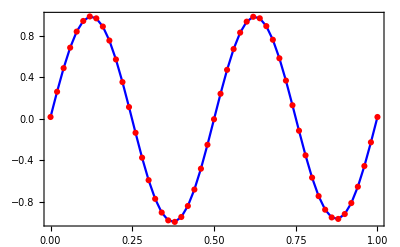

```mathematica
ParitySimulation=Table[Ω={{Ω1,Ω2},{Ω1,Ω2},{0,0},{0,0}};ν=1.45;δ={0+phi/t,0};ωIon=10;η=0.051;SimulationTime=4;TwoIonSimulation[Ω,δ,ν,MaxPhononNumber,SimulationTime,"Individual",Evaluate@(c[82]/.MSEvolution),0,True,False];{phi,Population[DensityMatrix[Evaluate[c[4.11/2]/.expoteSolution[[1]]]],1,MaxPhononNumber]+Population[DensityMatrix[Evaluate[c[4.11/2]/.expoteSolution[[1]]]],4,MaxPhononNumber]-Population[DensityMatrix[Evaluate[c[4.11/2]/.expoteSolution[[1]]]],3,MaxPhononNumber]-Population[DensityMatrix[Evaluate[c[4.11/2]/.expoteSolution[[1]]]],2,MaxPhononNumber]},{phi,0,1,1/50}];Show[ListLinePlot[#,PlotStyle->Blue,Frame->True],ListPlot[#,PlotStyle->Red]]&@ParitySimulation
```

## Example 2

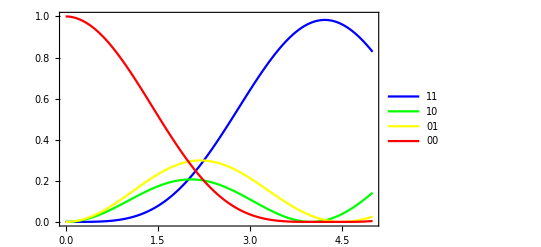

```mathematica
Ω={{1/(4*4.5),1/(4*4.0)},{1/(4*4.5),1/(4*4.0)},{0,0},{0,0}};δ={0,0};ω={ωIon-0.9ν,ωIon+0.9ν};ν=1.5;ωIon=10;η=0.1;SimulationTime=5;TwoIonSimulation[Ω,δ,ν,MaxPhononNumber,SimulationTime,"Individual"]
```

```mathematica
Ω={{1/(4*4.5),1/(4*4.0)},{1/(4*4.5),1/(4*4.0)},{1/(4*4.5),1/(4*4.0)},{1/(4*4.5),1/(4*4.0)}};δ={-ν+1/√(40*45),ν-1/√(40*45)};ω={ωIon-0.9ν,ωIon+0.9ν};ν=20;ωIon=10;η=0.1;SimulationTime=200;
TwoIonSimulation[Ω,δ,ν,MaxPhononNumber,SimulationTime,"Individual",Normalize[KroneckerProduct[{0,1},{0,1},{1,Table[0,{i,1,MaxPhononNumber}]}//Flatten]//Flatten],0,True]
MSEvolution=expoteSolution[[1]]
```

-Graphics-

{c→InterpolatingFunction[{{0., 200.}}, <>]}

```mathematica
s=Interpolation@Table[{at,Population[DensityMatrix[Evaluate[c[at]/.expoteSolution[[1]]]],1,MaxPhononNumber]+Population[DensityMatrix[Evaluate[c[at]/.expoteSolution[[1]]]],4,MaxPhononNumber]-Population[DensityMatrix[Evaluate[c[at]/.expoteSolution[[1]]]],3,MaxPhononNumber]-Population[DensityMatrix[Evaluate[c[at]/.expoteSolution[[1]]]],2,MaxPhononNumber]},{at,36,50}];NMaximize[{s[at],at<50&&at>40},at]
```

{0.999644,{at→41.95}}

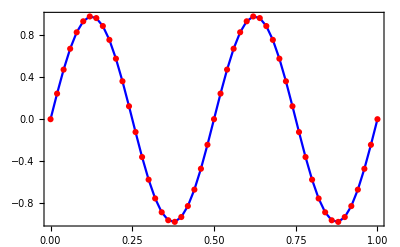

```mathematica
ParitySimulation=Table[Ω={{1/(4*4.5),1/(4*4.0)},{1/(4*4.5),1/(4*4.0)},{0,0},{0,0}};δ={phi/t,0};ω={ωIon-0.9ν,ωIon+0.9ν};ν=1.5;ωIon=10;η=0.1;SimulationTime=5;TwoIonSimulation[Ω,δ,ν,MaxPhononNumber,SimulationTime,"Individual",Evaluate@(c[41.950013298070466]/.MSEvolution),0,True,False];{phi,Population[DensityMatrix[Evaluate[c[2]/.expoteSolution[[1]]]],1,MaxPhononNumber]+Population[DensityMatrix[Evaluate[c[2]/.expoteSolution[[1]]]],4,MaxPhononNumber]-Population[DensityMatrix[Evaluate[c[2]/.expoteSolution[[1]]]],3,MaxPhononNumber]-Population[DensityMatrix[Evaluate[c[2]/.expoteSolution[[1]]]],2,MaxPhononNumber]},{phi,0,1,1/50}];Show[ListLinePlot[#,PlotStyle->Blue,Frame->True],ListPlot[#,PlotStyle->Red]]&@ParitySimulation
```

```mathematica
(Threshold[#,10^-2]&@ReducedSpinDensityMatrix[Evaluate@(c[41.950013298070466]/.MSEvolution)//Chop,MaxPhononNumber])//Chop//MatrixForm
```

(0.495283 | 0 | 0 | 0.000085749+0.499191 ⅈ
0 | 0 | 0 | 0
0 | 0 | 0 | 0
0.000085749-0.499191 ⅈ | 0 | 0 | 0.50454)

## Ising simulation

## Evolution of difference eigenstate of Pauli matrix

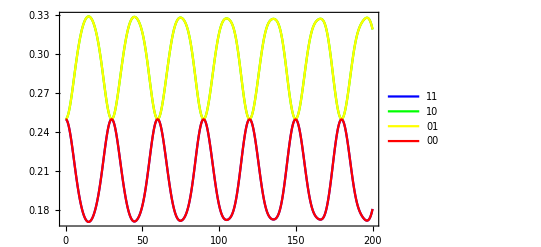

```mathematica
Ω={{1/(4*4.5),1/(4*4.0)},{1/(4*4.5),1/(4*4.0)},{1/(4*4.5),1/(4*4.0)},{1/(4*4.5),1/(4*4.0)}};δ={-ν+1/30,ν-1/30};ω={ωIon-0.9ν,ωIon+0.9ν};ν=20;ωIon=10;η=0.1;SimulationTime=200;
TwoIonSimulation[Ω,δ,ν,MaxPhononNumber,SimulationTime,"Individual",Normalize[KroneckerProduct[{1,-1},{1,1},{1,Table[0,{i,1,MaxPhononNumber}]}//Flatten]//Flatten]]
```

```mathematica
ClearAll[TwoIonSimulation]
```

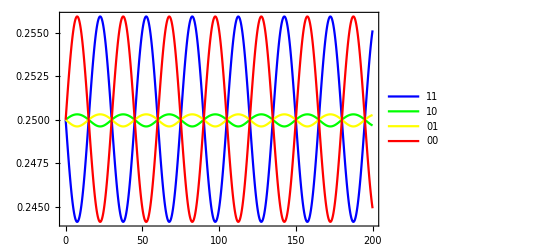

```mathematica
Ω={{1/(4*4.5),1/(4*4.0)},{1/(4*4.5),1/(4*4.0)},{1/(4*4.5),1/(4*4.0)},{1/(4*4.5),1/(4*4.0)}};δ={-ν+1/30,ν-1/30};ω={ωIon-0.9ν,ωIon+0.9ν};ν=20;ωIon=10;η=0.1;SimulationTime=200;
TwoIonSimulation[Ω,δ,ν,MaxPhononNumber,SimulationTime,"Individual",Normalize[KroneckerProduct[{1,I},{1,I},{1,Table[0,{i,1,MaxPhononNumber}]}//Flatten]//Flatten]]
```

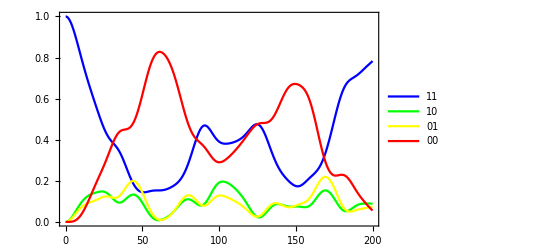

```mathematica
Ω={{1/(4*4.5),1/(4*4.0)},{1/(4*4.5),1/(4*4.0)},{1/(4*4.5),1/(4*4.0)},{1/(4*4.5),1/(4*4.0)}};δ={-ν+1/70,ν-1/70};ω={ωIon-0.9ν,ωIon+0.9ν};ν=20;ωIon=10;η=0.1;SimulationTime=200;
TwoIonSimulation[Ω,δ,ν,MaxPhononNumber,SimulationTime,"Individual",Normalize[KroneckerProduct[{1,0},{1,0},{1,Table[0,{i,1,MaxPhononNumber}]}//Flatten]//Flatten]]
```

## Adiabatic evolution

### Carrier

```mathematica
Ω={{1/(4*4.5),1/(4*4.0)},{1/(4*4.5),1/(4*4.0)},{0,0},{0,0}};δ={0,0};ω={ωIon-0.9ν,ωIon+0.9ν};ν=1;ωIon=10;η=0.1;SimulationTime=100;TwoIonSimulation[Ω,δ,ν,MaxPhononNumber,SimulationTime,"Total"]
```

-Graphics-

### Adiabatic evolution

#### If during the adiabatic evolution you also increases the Ising interaction from zero, the final state will be far away from be entangled. Only a mixed state.

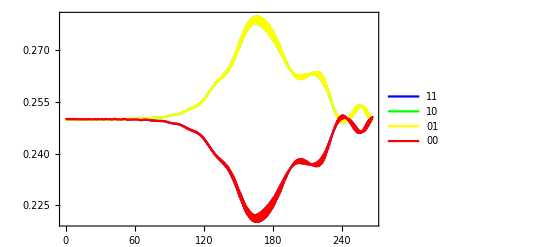

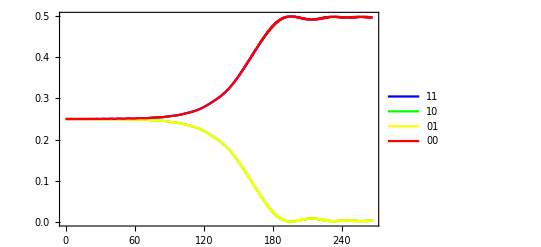

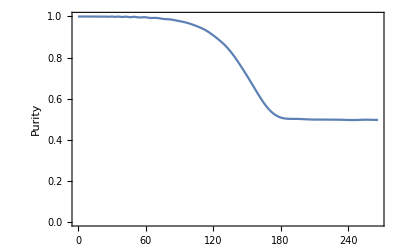

```mathematica
SimulationTime=2π √(40*45);NumofIons=2;Ω={{1/(4*4.5),1/(4*4.0)},{1/(4*4.5),1/(4*4.0)},{1/(4*4.5),1/(4*4.0)},{1/(4*4.5),1/(4*4.0)}};δ={-ν-1/√(2*40*45),ν+1/√(2*40*45)};ω={ωIon-0.9ν,ωIon+0.9ν};ν=20;ωIon=10;η=0.1;vi=1;
vf=5;Hamcar=∑_(ni=1)^2 2π Ω[[1,ni]]σP[ni].(-ⅈ η (a ⅇ^(-ⅈ 2π ν t)+adag ⅇ^(ⅈ 2π ν t) )+IdentityMatrix[4*(MaxPhononNumber+1)])+∑_(ni=1)^2 2π Ω[[2,ni]]σM[ni].(ⅈ (η a ⅇ^(-ⅈ 2π ν t)+η a† ⅇ^(ⅈ 2π ν t) )+IdentityMatrix[4*(MaxPhononNumber+1)])//Chop;
TwoIonSimulation[Exp[(vi+1)/SimulationTime t-vi]Ω,δ,ν,MaxPhononNumber,SimulationTime,"Individual",Normalize[KroneckerProduct[{1,1},{1,1},{1,Table[0,{i,1,MaxPhononNumber}]}//Flatten]//Flatten],Exp[-(vf+vi)/SimulationTime t+vi]Hamcar,True];AdiabaticEvolution=expoteSolution[[1]];
dataYRep=Table[{t,Population[DensityMatrix[SpinRotation[π/2,0].Evaluate[c[t]/.AdiabaticEvolution]],i,MaxPhononNumber]},{i,1,4},{t,0,SimulationTime,SimulationTime/pnt}];ListLinePlot[dataYRep,PlotStyle->({Thick,#}&/@{Blue,Green,Yellow,Red}),PlotLegends->{"11","10","01","00"},Frame->True,PlotRange->All]
ListLinePlot[Table[{t,Tr[MatrixPower[ReducedSpinDensityMatrix[Evaluate[c[t]/.AdiabaticEvolution],MaxPhononNumber],2]]//Chop},{t,0,SimulationTime,SimulationTime/300}],Frame->True,FrameLabel->"Purity"]
```

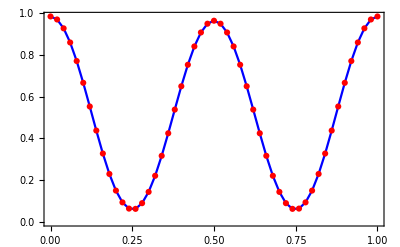

```mathematica
ParitySimulation=Table[Ω={{1/(4*4.5),1/(4*4.0)},{1/(4*4.5),1/(4*4.0)},{0,0},{0,0}};δ={phi/t,0};ω={ωIon-0.9ν,ωIon+0.9ν};ν=1.5;ωIon=10;η=0.1;SimulationTime=5;TwoIonSimulation[Ω,δ,ν,MaxPhononNumber,SimulationTime,"Individual",Evaluate[c[200]/.AdiabaticEvolution],0,True,False];{phi,Population[DensityMatrix[Evaluate[c[2]/.expoteSolution[[1]]]],1,MaxPhononNumber]+Population[DensityMatrix[Evaluate[c[2]/.expoteSolution[[1]]]],4,MaxPhononNumber]-Population[DensityMatrix[Evaluate[c[2]/.expoteSolution[[1]]]],3,MaxPhononNumber]-Population[DensityMatrix[Evaluate[c[2]/.expoteSolution[[1]]]],2,MaxPhononNumber]},{phi,0,1,1/50}];Show[ListLinePlot[#,PlotStyle->Blue,Frame->True],ListPlot[#,PlotStyle->Red]]&@ParitySimulation
```

```mathematica
(Threshold[#,10^-1]&@ReducedSpinDensityMatrix[Evaluate[c[250]/.AdiabaticEvolution],MaxPhononNumber])//Chop//MatrixForm
```

(0.247318 | 0 | 0 | -0.243126
0 | 0.252682 | 0.252662 | 0
0 | 0.252662 | 0.252682 | 0
-0.243126 | 0 | 0 | 0.247318)

#### If during the adiabatic evolution you keep Ising interaction constant, you can get an entangled state.

For the fully entangled states, Bell state, no matter we measure it on Z basis or Y basis, it will remain maximal entangled. Therefore, if the behavior in Z representation

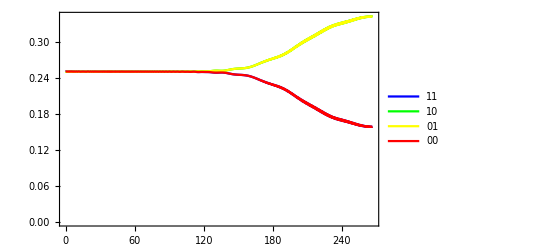

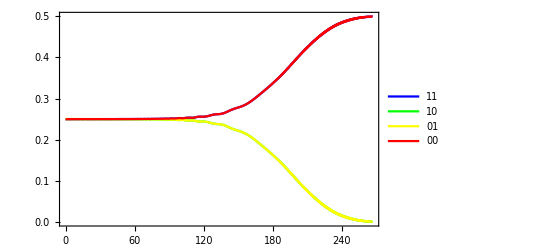

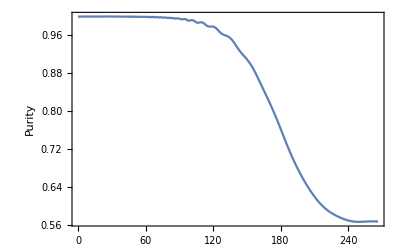

```mathematica
SimulationTime=2π √(40*45);NumofIons=2;Ω={{1/(4*4.5),1/(4*4.0)},{1/(4*4.5),1/(4*4.0)},{1/(4*4.5),1/(4*4.0)},{1/(4*4.5),1/(4*4.0)}};δ={-ν-1/√(2*40*45),ν+1/√(2*40*45)};ω={ωIon-0.9ν,ωIon+0.9ν};ν=20;ωIon=10; η=0.1;vi=3;
vf=5;Hamcar=∑_(ni=1)^2 2π Ω[[1,ni]]σP[ni].(-ⅈ η (a ⅇ^(-ⅈ 2π ν t)+adag ⅇ^(ⅈ 2π ν t) )+IdentityMatrix[4*(MaxPhononNumber+1)])+∑_(ni=1)^2 2π Ω[[2,ni]]σM[ni].(ⅈ (η a ⅇ^(-ⅈ 2π ν t)+η a† ⅇ^(ⅈ 2π ν t) )+IdentityMatrix[4*(MaxPhononNumber+1)])//Chop;
TwoIonSimulation[Ω,δ,ν,MaxPhononNumber,SimulationTime,"Individual",Normalize[KroneckerProduct[{1,1},{1,1},{1,Table[0,{i,1,MaxPhononNumber}]}//Flatten]//Flatten],Exp[-(vf+vi)/SimulationTime t+vi]Hamcar,True]
AdiabaticEvolution=expoteSolution[[1]];
dataYRep=Table[{t,Population[DensityMatrix[SpinRotation[π/2,0].Evaluate[c[t]/.AdiabaticEvolution]],i,MaxPhononNumber]},{i,1,4},{t,0,SimulationTime,SimulationTime/pnt}];ListLinePlot[dataYRep,PlotStyle->({Thick,#}&/@{Blue,Green,Yellow,Red}),PlotLegends->{"11","10","01","00"},Frame->True,PlotRange->All]
ListLinePlot[Table[{t,Tr[MatrixPower[ReducedSpinDensityMatrix[Evaluate[c[t]/.AdiabaticEvolution],MaxPhononNumber],2]]//Chop},{t,0,SimulationTime,SimulationTime/300}],Frame->True,FrameLabel->"Purity"]
```

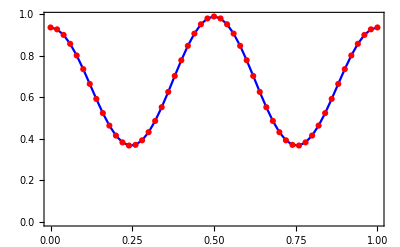

```mathematica
ParitySimulation=Table[Ω={{1/(4*4.5),1/(4*4.0)},{1/(4*4.5),1/(4*4.0)},{0,0},{0,0}};δ={phi/t,0};ω={ωIon-0.9ν,ωIon+0.9ν};ν=1.5;ωIon=10;η=0.1;SimulationTime=5;TwoIonSimulation[Ω,δ,ν,MaxPhononNumber,SimulationTime,"Individual",Evaluate[c[250]/.AdiabaticEvolution],0,True,False];{phi,Population[DensityMatrix[Evaluate[c[2]/.expoteSolution[[1]]]],1,MaxPhononNumber]+Population[DensityMatrix[Evaluate[c[2]/.expoteSolution[[1]]]],4,MaxPhononNumber]-Population[DensityMatrix[Evaluate[c[2]/.expoteSolution[[1]]]],3,MaxPhononNumber]-Population[DensityMatrix[Evaluate[c[2]/.expoteSolution[[1]]]],2,MaxPhononNumber]},{phi,0,1,1/50}];Show[ListLinePlot[#,PlotStyle->Blue,Frame->True],ListPlot[#,PlotStyle->Red]]&@ParitySimulation
```

```mathematica
(Threshold[#,10^-1]&@ReducedSpinDensityMatrix[Evaluate[c[250]/.AdiabaticEvolution],MaxPhononNumber])//Chop//MatrixForm
```

(0.162857 | 0 | 0 | -0.151917
0 | 0.337143 | 0.337085 | 0
0 | 0.337085 | 0.337143 | 0
-0.151917 | 0 | 0 | 0.162857)

### Ideal adiabatic evolution

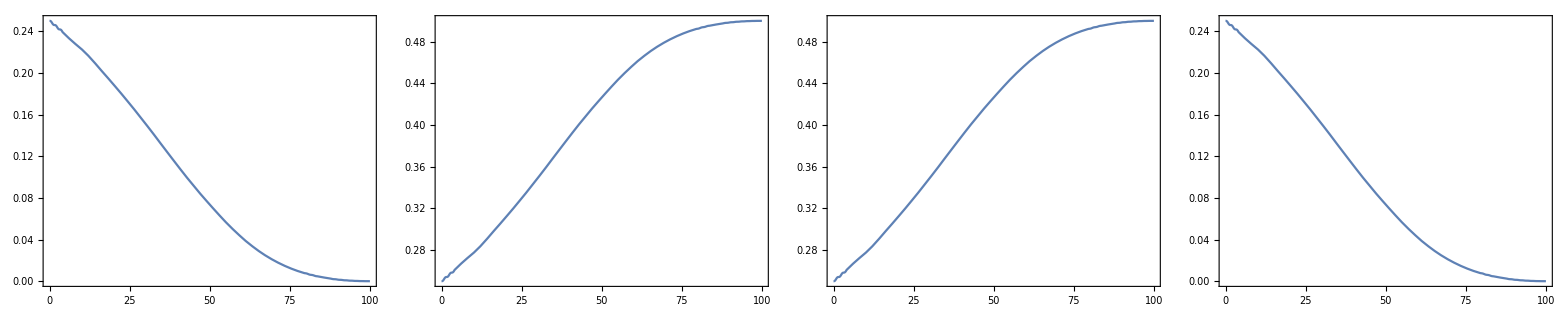

```mathematica
AdiabaticEvolution[100,2]
```

### Bang-bang evolution

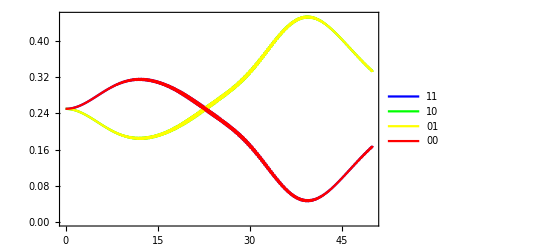

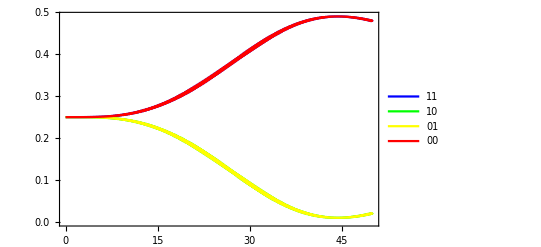

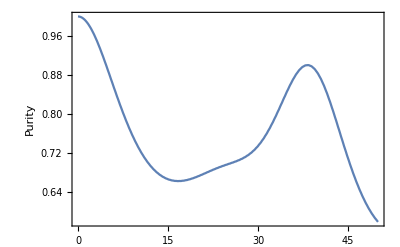

```mathematica
SimulationTime=50;NumofIons=2;Ω={{1/(4*4.5),1/(4*4.0)},{1/(4*4.5),1/(4*4.0)},{1/(4*4.5),1/(4*4.0)},{1/(4*4.5),1/(4*4.0)}};δ={-ν-1/√(40*45),ν+1/√(40*45)};ω={ωIon-0.9ν,ωIon+0.9ν};ν=20;ωIon=10;η=0.1;vi=6;
vf=10;
Hamcar=∑_(ni=1)^2 2π Ω[[1,ni]]σP[ni].(-ⅈ η (a ⅇ^(-ⅈ 2π ν t)+adag ⅇ^(ⅈ 2π ν t) )+IdentityMatrix[4*(MaxPhononNumber+1)])+∑_(ni=1)^2 2π Ω[[2,ni]]σM[ni].(ⅈ (η a ⅇ^(-ⅈ 2π ν t)+η a† ⅇ^(ⅈ 2π ν t) )+IdentityMatrix[4*(MaxPhononNumber+1)])//Chop;
TwoIonSimulation[Ω,δ,ν,MaxPhononNumber,SimulationTime,"Individual",Normalize[KroneckerProduct[{1,1},{1,1},{1,Table[0,{i,1,MaxPhononNumber}]}//Flatten]//Flatten],Exp[-3.1]Hamcar,True];BangBangEvolution=expoteSolution[[1]];
dataYRep=Table[{t,Population[DensityMatrix[SpinRotation[π/2,0].Evaluate[c[t]/.BangBangEvolution]],i,MaxPhononNumber]},{i,1,4},{t,0,SimulationTime,SimulationTime/pnt}];ListLinePlot[dataYRep,PlotStyle->({Thick,#}&/@{Blue,Green,Yellow,Red}),PlotLegends->{"11","10","01","00"},Frame->True,PlotRange->All]
ListLinePlot[Table[{t,Tr[MatrixPower[ReducedSpinDensityMatrix[Evaluate[c[t]/.BangBangEvolution],MaxPhononNumber],2]]//Chop},{t,0,SimulationTime,SimulationTime/300}],Frame->True,FrameLabel->"Purity"]
```

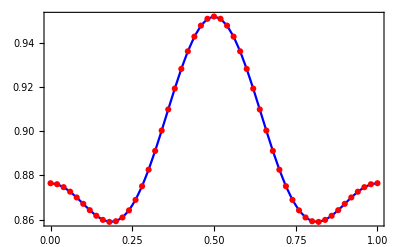

```mathematica
ParitySimulation=Table[Ω={{1/(4*4.5),1/(4*4.0)},{1/(4*4.5),1/(4*4.0)},{0,0},{0,0}};δ={phi/t,0};ω={ωIon-0.9ν,ωIon+0.9ν};ν=1.5;ωIon=10;η=0.1;SimulationTime=5;TwoIonSimulation[Ω,δ,ν,MaxPhononNumber,SimulationTime,"Individual",Evaluate[c[40]/.BangBangEvolution],0,True,False];{phi,Population[DensityMatrix[Evaluate[c[2]/.expoteSolution[[1]]]],1,MaxPhononNumber]+Population[DensityMatrix[Evaluate[c[2]/.expoteSolution[[1]]]],4,MaxPhononNumber]-Population[DensityMatrix[Evaluate[c[2]/.expoteSolution[[1]]]],3,MaxPhononNumber]-Population[DensityMatrix[Evaluate[c[2]/.expoteSolution[[1]]]],2,MaxPhononNumber]},{phi,0,1,1/50}];Show[ListLinePlot[#,PlotStyle->Blue,Frame->True],ListPlot[#,PlotStyle->Red]]&@ParitySimulation
```

```mathematica
(Threshold[#,10^-2]&@ReducedSpinDensityMatrix[Evaluate[c[40]/.BangBangEvolution],MaxPhononNumber])//Chop//MatrixForm
```

(0.047878 | 0.0673955-0.0538315 ⅈ | 0.0676318-0.0562626 ⅈ | -0.01252
0.0673955+0.0538315 ⅈ | 0.452122 | 0.452021 | 0.0676318+0.0562626 ⅈ
0.0676318+0.0562626 ⅈ | 0.452021 | 0.452122 | 0.0673955+0.0538315 ⅈ
-0.01252 | 0.0676318-0.0562626 ⅈ | 0.0673955-0.0538315 ⅈ | 0.047878)

## Real experiment sequency

### Prepare the eigenstate of MS interaction

```mathematica
Ω={{1/(4*4.5),1/(4*4.0)},{1/(4*4.5),1/(4*4.0)},{0,0},{0,0}};δ={0,0};ω={ωIon-0.9ν,ωIon+0.9ν};ν=1.5;ωIon=10;η=0.1;SimulationTime=4;TwoIonSimulation[Ω,δ,ν,MaxPhononNumber,SimulationTime,"Individual",Normalize[KroneckerProduct[{0,1},{0,1},{1,Table[0,{i,1,MaxPhononNumber}]}//Flatten]//Flatten],0,True];FirstRotation=expoteSolution[[1]]
```

-Graphics-

{c→InterpolatingFunction[{{0., 4.}}, <>]}

### Test whether this is the eigenstate of MS interaction

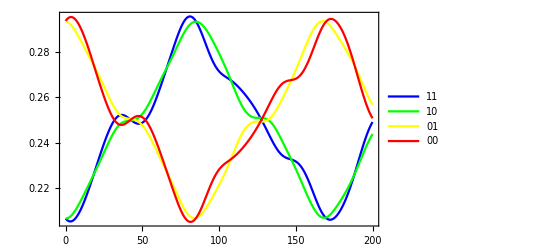

```mathematica
Ω={{1/(4*4.5),1/(4*4.0)},{1/(4*4.5),1/(4*4.0)},{1/(4*4.5),1/(4*4.0)},{1/(4*4.5),1/(4*4.0)}};δ={-ν+1/√(40*45),ν-1/√(40*45)};ω={ωIon-0.9ν,ωIon+0.9ν};ν=20;ωIon=10;η=0.1;SimulationTime=200;
TwoIonSimulation[Ω,δ,ν,MaxPhononNumber,SimulationTime,"Individual",Evaluate@(c[2]/.FirstRotation),0,True]
```

### Prepare the eigenstate of carrier

```mathematica
Ω={{1/(4*4.5),1/(4*4.0)},{1/(4*4.5),1/(4*4.0)},{0,0},{0,0}};δ={1/(4t),0};ω={ωIon-0.9ν,ωIon+0.9ν};ν=1.5;ωIon=10;η=0.1;SimulationTime=4;TwoIonSimulation[Ω,δ,ν,MaxPhononNumber,SimulationTime,"Individual",Normalize[KroneckerProduct[{0,1},{0,1},{1,Table[0,{i,1,MaxPhononNumber}]}//Flatten]//Flatten],0,True];SecondRotation=expoteSolution[[1]]
```

-Graphics-

{c→InterpolatingFunction[{{0., 4.}}, <>]}

### Test whether this is the eigenstate of carrier

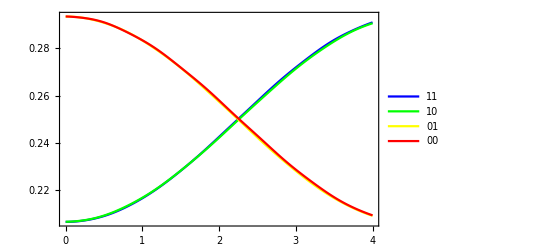

{c→InterpolatingFunction[{{0., 4.}}, <>]}

```mathematica
Ω={{1/(4*4.5),1/(4*4.0)},{1/(4*4.5),1/(4*4.0)},{0,0},{0,0}};δ={0,0};ω={ωIon-0.9ν,ωIon+0.9ν};ν=1.5;ωIon=10;η=0.1;SimulationTime=4;TwoIonSimulation[Ω,δ,ν,MaxPhononNumber,SimulationTime,"Individual",Evaluate@(c[2]/.SecondRotation),0,True];FirstRotation=expoteSolution[[1]]
```

### Adiabatic evolution

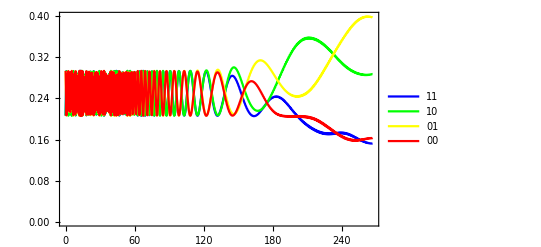

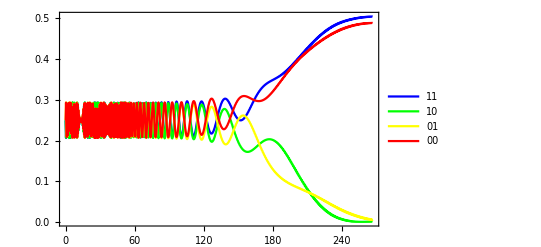

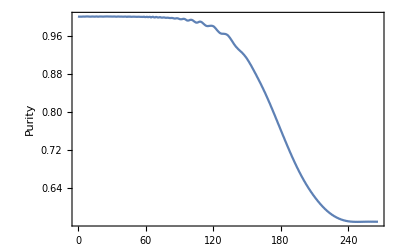

```mathematica
SimulationTime=2π √(40*45);NumofIons=2;Ω={{1/(4*4.5),1/(4*4.0)},{1/(4*4.5),1/(4*4.0)},{1/(4*4.5),1/(4*4.0)},{1/(4*4.5),1/(4*4.0)}};δ={-ν-1/√(2*40*45),ν+1/√(2*40*45)};ω={ωIon-0.9ν,ωIon+0.9ν};ν=20;ωIon=10; η=0.1;vi=3;
vf=5;Hamcar=∑_(ni=1)^2 2π Ω[[1,ni]]σP[ni].(-ⅈ η (a ⅇ^(-ⅈ 2π ν t)+adag ⅇ^(ⅈ 2π ν t) )+IdentityMatrix[4*(MaxPhononNumber+1)])+∑_(ni=1)^2 2π Ω[[2,ni]]σM[ni].(ⅈ (η a ⅇ^(-ⅈ 2π ν t)+η a† ⅇ^(ⅈ 2π ν t) )+IdentityMatrix[4*(MaxPhononNumber+1)])//Chop;
TwoIonSimulation[Ω,δ,ν,MaxPhononNumber,SimulationTime,"Individual",Evaluate@(c[2]/.SecondRotation),Exp[-(vf+vi)/SimulationTime t+vi]Hamcar,True];AdiabaticEvolution=expoteSolution[[1]];
dataYRep=Table[{t,Population[DensityMatrix[SpinRotation[π/2,0].Evaluate[c[t]/.AdiabaticEvolution]],i,MaxPhononNumber]},{i,1,4},{t,0,SimulationTime,SimulationTime/pnt}];ListLinePlot[dataYRep,PlotStyle->({Thick,#}&/@{Blue,Green,Yellow,Red}),PlotLegends->{"11","10","01","00"},Frame->True,PlotRange->All]
ListLinePlot[Table[{t,Tr[MatrixPower[ReducedSpinDensityMatrix[Evaluate[c[t]/.AdiabaticEvolution],MaxPhononNumber],2]]//Chop},{t,0,SimulationTime,SimulationTime/300}],Frame->True,FrameLabel->"Purity"]
```

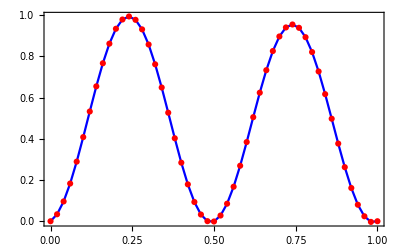

```mathematica
ParitySimulation=Table[Ω={{1/(4*4.5),1/(4*4.0)},{1/(4*4.5),1/(4*4.0)},{0,0},{0,0}};δ={phi/t,0};ω={ωIon-0.9ν,ωIon+0.9ν};ν=1.5;ωIon=10;η=0.1;SimulationTime=5;TwoIonSimulation[Ω,δ,ν,MaxPhononNumber,SimulationTime,"Individual",Evaluate[c[SimulationTime]/.AdiabaticEvolution],0,True,False];{phi,Population[DensityMatrix[Evaluate[c[2]/.expoteSolution[[1]]]],1,MaxPhononNumber]+Population[DensityMatrix[Evaluate[c[2]/.expoteSolution[[1]]]],4,MaxPhononNumber]-Population[DensityMatrix[Evaluate[c[2]/.expoteSolution[[1]]]],3,MaxPhononNumber]-Population[DensityMatrix[Evaluate[c[2]/.expoteSolution[[1]]]],2,MaxPhononNumber]},{phi,0,1,1/50}];Show[ListLinePlot[#,PlotStyle->Blue,Frame->True],ListPlot[#,PlotStyle->Red]]&@ParitySimulation
```

### Bang-bang evolution

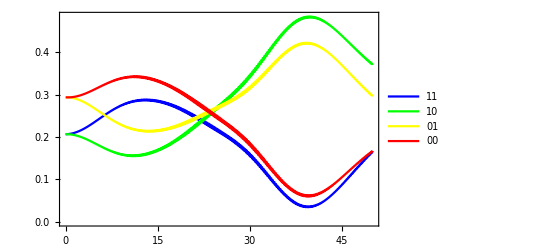

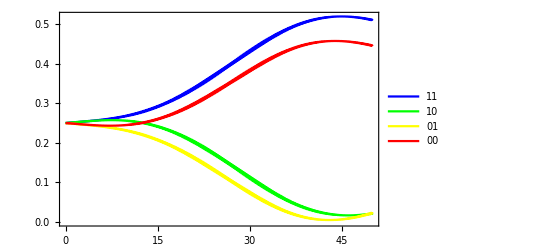

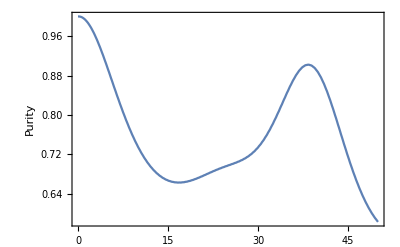

```mathematica
SimulationTime=50;NumofIons=2;Ω={{1/(4*4.5),1/(4*4.0)},{1/(4*4.5),1/(4*4.0)},{1/(4*4.5),1/(4*4.0)},{1/(4*4.5),1/(4*4.0)}};δ={-ν-1/√(40*45),ν+1/√(40*45)};ω={ωIon-0.9ν,ωIon+0.9ν};ν=20;ωIon=10;η=0.1;vi=6;
vf=10;
Hamcar=∑_(ni=1)^2 2π Ω[[1,ni]]σP[ni].(-ⅈ η (a ⅇ^(-ⅈ 2π ν t)+adag ⅇ^(ⅈ 2π ν t) )+IdentityMatrix[4*(MaxPhononNumber+1)])+∑_(ni=1)^2 2π Ω[[2,ni]]σM[ni].(ⅈ (η a ⅇ^(-ⅈ 2π ν t)+η a† ⅇ^(ⅈ 2π ν t) )+IdentityMatrix[4*(MaxPhononNumber+1)])//Chop;
TwoIonSimulation[Ω,δ,ν,MaxPhononNumber,SimulationTime,"Individual",Evaluate@(c[2]/.SecondRotation),Exp[-3.1]Hamcar,True];BangBangEvolution=expoteSolution[[1]];
dataYRep=Table[{t,Population[DensityMatrix[SpinRotation[π/2,0].Evaluate[c[t]/.BangBangEvolution]],i,MaxPhononNumber]},{i,1,4},{t,0,SimulationTime,SimulationTime/pnt}];ListLinePlot[dataYRep,PlotStyle->({Thick,#}&/@{Blue,Green,Yellow,Red}),PlotLegends->{"11","10","01","00"},Frame->True,PlotRange->All]
ListLinePlot[Table[{t,Tr[MatrixPower[ReducedSpinDensityMatrix[Evaluate[c[t]/.BangBangEvolution],MaxPhononNumber],2]]//Chop},{t,0,SimulationTime,SimulationTime/300}],Frame->True,FrameLabel->"Purity"]
```

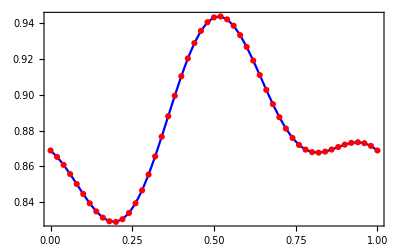

```mathematica
ParitySimulation=Table[Ω={{1/(4*4.5),1/(4*4.0)},{1/(4*4.5),1/(4*4.0)},{0,0},{0,0}};δ={phi/t,0};ω={ωIon-0.9ν,ωIon+0.9ν};ν=1.5;ωIon=10;η=0.1;SimulationTime=5;TwoIonSimulation[Ω,δ,ν,MaxPhononNumber,SimulationTime,"Individual",Evaluate[c[40]/.BangBangEvolution],0,True,False];{phi,Population[DensityMatrix[Evaluate[c[2]/.expoteSolution[[1]]]],1,MaxPhononNumber]+Population[DensityMatrix[Evaluate[c[2]/.expoteSolution[[1]]]],4,MaxPhononNumber]-Population[DensityMatrix[Evaluate[c[2]/.expoteSolution[[1]]]],3,MaxPhononNumber]-Population[DensityMatrix[Evaluate[c[2]/.expoteSolution[[1]]]],2,MaxPhononNumber]},{phi,0,1,1/50}];Show[ListLinePlot[#,PlotStyle->Blue,Frame->True],ListPlot[#,PlotStyle->Red]]&@ParitySimulation
```

```mathematica
(Threshold[#,10^-1]&@ReducedSpinDensityMatrix[Evaluate[c[40]/.BangBangEvolution],MaxPhononNumber])//Chop//MatrixForm
```

## Adiabatic evolution meanwhile maintain the coherence

# Analytic Simulation

## Parity measurement

```mathematica
Manipulate[AnalyticParityEvolve[({{0.5, 0, 0, -0.5I}, {0, 0, 0, 0}, {0, 0, 0, 0}, {0.5I, 0, 0, 0.5}}),a,b],{a,0,2π},{b,0,2π}]
```

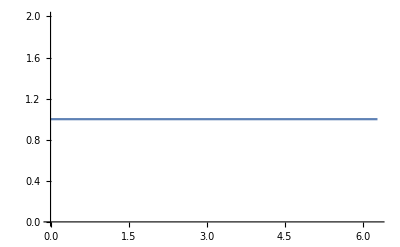

```mathematica
AnalyticParityEvolve[({{0, 0, 0, 0}, {0, 0.5, 0.5, 0}, {0, 0.5, 0.5, 0}, {0, 0, 0, 0}}),π/2,π/2]
```

# Multi-mode Simulation

## Pre-function

## Basic Function

```mathematica
SpinEigenstate={{1,0},{0,1}};PhononEigenstate[n_]:=Module[{circle},circle=Table[i,{i,1,n+1}];Table[Nest[Permute[#,Cycles[{circle}]]&,{Table[0,{i,1,n}],1}//Flatten,j],{j,1,n+1}]];
```

```mathematica
DensityMatrix[State_]:=Outer[Times,Conjugate@State,State]/(Conjugate@State.State)
```

```mathematica
ReducedSpinDensityMatrix[State_,PhononNumber_]:=Module[{wholeDensityMatrix},wholeDensityMatrix=DensityMatrix[State];Table[Sum[(Normalize@Flatten[KroneckerProduct[Nest[Permute[#,Cycles[{{1,2,3,4}}]]&,{0,0,0,1},i],PhononEigenstate[PhononNumber][[p]]]]).wholeDensityMatrix.(Normalize@Flatten@KroneckerProduct[Nest[Permute[#,Cycles[{{1,2,3,4}}]]&,{0,0,0,1},j],PhononEigenstate[PhononNumber][[p]]]),{p,1,PhononNumber+1}]//Chop,{i,1,4},{j,1,4}]]
```

```mathematica
PopulationSingleParticle[M_,g_,PhononNumber_]:=Sum[(Normalize@Flatten[KroneckerProduct[Nest[Permute[#,Cycles[{{1,2}}]]&,{0,1},g],PhononEigenstate[PhononNumber][[p]]]]).M.(Normalize@Flatten@KroneckerProduct[Nest[Permute[#,Cycles[{{1,2}}]]&,{0,1},g],PhononEigenstate[PhononNumber][[p]]]),{p,1,PhononNumber+1}]//Chop
```

```mathematica
Population[M_,g_,PhononNumber_]:=Sum[(Normalize@Flatten[KroneckerProduct[Nest[Permute[#,Cycles[{{1,2,3,4}}]]&,{0,0,0,1},g],PhononEigenstate[PhononNumber][[p]]]]).M.(Normalize@Flatten@KroneckerProduct[Nest[Permute[#,Cycles[{{1,2,3,4}}]]&,{0,0,0,1},g],PhononEigenstate[PhononNumber][[p]]]),{p,1,PhononNumber+1}]//Chop
```

```mathematica
PhononDistribution[M_,g_,PhononNumber_]:=Sum[(Normalize@Flatten[KroneckerProduct[Nest[Permute[#,Cycles[{{1,2,3,4}}]]&,{0,0,0,1},p],PhononEigenstate[PhononNumber][[g]]]]).M.(Normalize@Flatten@KroneckerProduct[Nest[Permute[#,Cycles[{{1,2,3,4}}]]&,{0,0,0,1},p],PhononEigenstate[PhononNumber][[g]]]),{p,1,4}]//Chop
```

```mathematica
UParity[ϕ_,θ_]=({{Cos[θ/2], -I E^(I ϕ)Sin[θ/2]}, {-I E^(-I ϕ)Sin[θ/2], Cos[θ/2]}})
```

{{Cos[θ/2],-ⅈ ⅇ^(ⅈ ϕ) Sin[θ/2]},{-ⅈ ⅇ^(-ⅈ ϕ) Sin[θ/2],Cos[θ/2]}}

```mathematica
UParityTwoIon[ϕ_,θ1_,θ2_]=KroneckerProduct[UParity[ϕ,θ1],UParity[ϕ,θ2]]
```

{{Cos[θ1/2] Cos[θ2/2],-ⅈ ⅇ^(ⅈ ϕ) Cos[θ1/2] Sin[θ2/2],-ⅈ ⅇ^(ⅈ ϕ) Cos[θ2/2] Sin[θ1/2],-ⅇ^(2 ⅈ ϕ) Sin[θ1/2] Sin[θ2/2]},{-ⅈ ⅇ^(-ⅈ ϕ) Cos[θ1/2] Sin[θ2/2],Cos[θ1/2] Cos[θ2/2],-Sin[θ1/2] Sin[θ2/2],-ⅈ ⅇ^(ⅈ ϕ) Cos[θ2/2] Sin[θ1/2]},{-ⅈ ⅇ^(-ⅈ ϕ) Cos[θ2/2] Sin[θ1/2],-Sin[θ1/2] Sin[θ2/2],Cos[θ1/2] Cos[θ2/2],-ⅈ ⅇ^(ⅈ ϕ) Cos[θ1/2] Sin[θ2/2]},{-ⅇ^(-2 ⅈ ϕ) Sin[θ1/2] Sin[θ2/2],-ⅈ ⅇ^(-ⅈ ϕ) Cos[θ2/2] Sin[θ1/2],-ⅈ ⅇ^(-ⅈ ϕ) Cos[θ1/2] Sin[θ2/2],Cos[θ1/2] Cos[θ2/2]}}

```mathematica
AnalyticParityEvolve[ρ_,θ1_,θ2_]:=Module[{ρAfterParity},ρAfterParity=Refine[ComplexExpand@(UParityTwoIon[ϕ,θ1,θ2].ρ.UParityTwoIon[ϕ,θ1,θ2]†),ϕ∈Reals]//Chop//FullSimplify;Plot[ρAfterParity[[1,1]]+ρAfterParity[[4,4]]-ρAfterParity[[2,2]]-ρAfterParity[[3,3]],{ϕ,0,2π}]]
```

## Basic Matrixs

```mathematica
MaxPhononNumber=4;
```

```mathematica
Id={{1,0},{0,1}};
Px={{0,1},{1,0}};
Py={{0,-ⅈ},{ⅈ,0}};
Pz={{1,0},{0,-1}};
Pm={{0,1},{0,0}};
Pp={{0,0},{1,0}};
σx[j_]:=KroneckerProduct[IdentityMatrix[ 2^(NumofIons-j)],KroneckerProduct[Px,IdentityMatrix[ 2^(j-1)]]]
σy[j_]:=KroneckerProduct[IdentityMatrix[ 2^(NumofIons-j)],KroneckerProduct[Py,IdentityMatrix[ 2^(j-1)]]]
σz[j_]:=KroneckerProduct[IdentityMatrix[ 2^(NumofIons-j)],KroneckerProduct[Pz,IdentityMatrix[ 2^(j-1)]]]
σp[j_]:=KroneckerProduct[IdentityMatrix[ 2^(NumofIons-j)],KroneckerProduct[Pp,IdentityMatrix[ 2^(j-1)]]]
σm[j_]:=KroneckerProduct[IdentityMatrix[ 2^(NumofIons-j)],KroneckerProduct[Pm,IdentityMatrix[ 2^(j-1)]]]
```

```mathematica
Subscript[σ, x]=({{0, 1}, {1, 0}});Subscript[σ, z]=({{1, 0}, {0, -1}});Subscript[σ, y]=({{0, -I}, {I, 0}});SubPlus[σ]=({{0, 1}, {0, 0}});SubMinus[σ]=({{0, 0}, {1, 0}});a=KroneckerProduct[IdentityMatrix[2],IdentityMatrix[2],Table[KroneckerDelta[i,j-1] √j,{i,0,MaxPhononNumber},{j,0,MaxPhononNumber}],IdentityMatrix[MaxPhononNumber+1]];adag=KroneckerProduct[IdentityMatrix[2],IdentityMatrix[2],Table[KroneckerDelta[i,j+1] √(j+1),{i,0,MaxPhononNumber},{j,0,MaxPhononNumber}],IdentityMatrix[MaxPhononNumber+1]];b=KroneckerProduct[IdentityMatrix[2],IdentityMatrix[2],IdentityMatrix[MaxPhononNumber+1],Table[KroneckerDelta[i,j-1] √j,{i,0,MaxPhononNumber},{j,0,MaxPhononNumber}]];bdag=KroneckerProduct[IdentityMatrix[2],IdentityMatrix[2],IdentityMatrix[MaxPhononNumber+1],Table[KroneckerDelta[i,j+1] √(j+1),{i,0,MaxPhononNumber},{j,0,MaxPhononNumber}]];
```

```mathematica
SpinRotation[θ_,φ_]:=MatrixExp[KroneckerProduct[-ⅈ θ/2((∑_(k=1)^NumofIons σx[k])Cos[φ]+(∑_(k=1)^NumofIons σy[k])Sin[φ]),IdentityMatrix[MaxPhononNumber+1]]]
```

```mathematica
σZ[i_]:=KroneckerProduct@@Flatten[{Nest[Permute[#,Cycles[{{1,2}}]]&,{IdentityMatrix[2],Subscript[σ, z]},i],{IdentityMatrix[(MaxPhononNumber+1)^2]}},1]
```

```mathematica
σP[i_]:=KroneckerProduct@@Flatten[{Nest[Permute[#,Cycles[{{1,2}}]]&,{IdentityMatrix[2],SubPlus[σ]},i],{IdentityMatrix[(MaxPhononNumber+1)^2]}},1]
```

```mathematica
σM[i_]:=KroneckerProduct@@Flatten[{Nest[Permute[#,Cycles[{{1,2}}]]&,{IdentityMatrix[2],SubMinus[σ]},i],{IdentityMatrix[(MaxPhononNumber+1)^2]}},1]
```

```mathematica
pnt=800;TwoIonSimulationTwoMode[Ω_,δ_,ν_,MaxPhononNumber_,SimulationTime_,only_,initialState_: Normalize[KroneckerProduct[{0,1},{0,1},{1,Table[0,{i,1,MaxPhononNumber}]}//Flatten,{1,Table[0,{i,1,MaxPhononNumber}]}//Flatten]//Flatten],Hamcar_:0,export_:False,plotTrue_:True]:=Module[{IHamiltonian,a,adag,b,bdag,σZ,σP,σM,sol,data,Hambsb,Hamrsb,δωb,δωr,end},δωb=2π δ[[1]];δωr=2π δ[[2]];a=KroneckerProduct[IdentityMatrix[2],IdentityMatrix[2],Table[KroneckerDelta[i,j-1] √j,{i,0,MaxPhononNumber},{j,0,MaxPhononNumber}],IdentityMatrix[MaxPhononNumber+1]];adag=KroneckerProduct[IdentityMatrix[2],IdentityMatrix[2],Table[KroneckerDelta[i,j+1] √(j+1),{i,0,MaxPhononNumber},{j,0,MaxPhononNumber}],IdentityMatrix[MaxPhononNumber+1]];b=KroneckerProduct[IdentityMatrix[2],IdentityMatrix[2],IdentityMatrix[MaxPhononNumber+1],Table[KroneckerDelta[i,j-1] √j,{i,0,MaxPhononNumber},{j,0,MaxPhononNumber}]];bdag=KroneckerProduct[IdentityMatrix[2],IdentityMatrix[2],IdentityMatrix[MaxPhononNumber+1],Table[KroneckerDelta[i,j+1] √(j+1),{i,0,MaxPhononNumber},{j,0,MaxPhononNumber}]];σZ[i_]:=KroneckerProduct@@Flatten[{Nest[Permute[#,Cycles[{{1,2}}]]&,{IdentityMatrix[2],Subscript[σ, z]},i],{IdentityMatrix[(MaxPhononNumber+1)^2]}},1];σP[i_]:=KroneckerProduct@@Flatten[{Nest[Permute[#,Cycles[{{1,2}}]]&,{IdentityMatrix[2],SubPlus[σ]},i],{IdentityMatrix[(MaxPhononNumber+1)^2]}},1];σM[i_]:=KroneckerProduct@@Flatten[{Nest[Permute[#,Cycles[{{1,2}}]]&,{IdentityMatrix[2],SubMinus[σ]},i],{IdentityMatrix[(MaxPhononNumber+1)^2]}},1];Hambsb=∑_(ni=1)^2 2π Ω[[1,ni]]σP[ni].(-ⅈ η (a ⅇ^(-ⅈ 2π ν[[1]] t)+adag ⅇ^(ⅈ 2π ν[[1]] t)+b ⅇ^(-ⅈ 2π ν[[2]] t)+bdag ⅇ^(ⅈ 2π ν[[2]] t) )+IdentityMatrix[4*(MaxPhononNumber+1)^2])*ⅇ^(ⅈ δωb  t)+∑_(ni=1)^2 2π Ω[[2,ni]]σM[ni].(ⅈ η (a ⅇ^(-ⅈ 2π ν[[1]] t)+adag ⅇ^(ⅈ 2π ν[[1]] t)+b ⅇ^(-ⅈ 2π ν[[2]] t)+bdag ⅇ^(ⅈ 2π ν[[2]] t) )+IdentityMatrix[4*(MaxPhononNumber+1)^2])*ⅇ^(-ⅈ δωb  t)//Chop//Simplify;Hamrsb=∑_(ni=1)^2 2π Ω[[3,ni]]σP[ni].(-ⅈ η (a ⅇ^(-ⅈ 2π ν[[1]] t)+adag ⅇ^(ⅈ 2π ν[[1]] t)+b ⅇ^(-ⅈ 2π ν[[2]] t)+bdag ⅇ^(ⅈ 2π ν[[2]] t) )+IdentityMatrix[4*(MaxPhononNumber+1)^2])*ⅇ^(ⅈ δωr  t)+∑_(ni=1)^2 2π Ω[[4,ni]]σM[ni].(ⅈ η (a ⅇ^(-ⅈ 2π ν[[1]] t)+adag ⅇ^(ⅈ 2π ν[[1]] t)+b ⅇ^(-ⅈ 2π ν[[2]] t)+bdag ⅇ^(ⅈ 2π ν[[2]] t) )+IdentityMatrix[4*(MaxPhononNumber+1)^2])*ⅇ^(-ⅈ δωr  t)//Chop//Simplify;IHamiltonian=Hambsb+Hamrsb+Hamcar;sol=NDSolve[{I D[c[t],t]==(IHamiltonian).c[t],c[0]==initialState},c,{t,0,SimulationTime},MaxSteps->Infinity](*;If[export,expoteSolution=sol];If[plotTrue==False,Goto[end]];If[only=="Individual",data=Table[{t,Population[DensityMatrix[Evaluate[c[t]/.sol[[1]]]],i,(MaxPhononNumber+1)^2-1]},{i,1,4},{t,0,SimulationTime,SimulationTime/pnt}];Print[ListLinePlot[data,PlotStyle->({Thick,#}&/@{Blue,Green,Yellow,Red}),PlotLegends->{"11","10","01","00"},Frame->True,PlotRange->All]],data=Table[{t,2Population[DensityMatrix[Evaluate[c[t]/.sol[[1]]]],1,(MaxPhononNumber+1)^2-1]+Population[DensityMatrix[Evaluate[c[t]/.sol[[1]]]],2,(MaxPhononNumber+1)^2-1]+Population[DensityMatrix[Evaluate[c[t]/.sol[[1]]]],3,(MaxPhononNumber+1)^2-1]},{t,0,SimulationTime,SimulationTime/pnt}];Print[ListLinePlot[data,Frame->True,PlotStyle->Blue]]];Label[end];*)]
```

## Simulation

```mathematica
Clear[TwoIonSimulationTwoMode]
```

```mathematica
Ω={{1/(4*4.5),0},{1/(4*4.5),0},{0,0},{0,0}};δ={0,0};ω={ωIon-0.9ν,ωIon+0.9ν};ν={20,10};ωIon=10;η=0.1;SimulationTime=200;solution=TwoIonSimulationTwoMode[Ω,δ,ν,MaxPhononNumber,SimulationTime,"Individual"]
```

{{c→InterpolatingFunction[{{0., 200.}}, <>]}}

```mathematica
Table[{t,2Population[DensityMatrix[Evaluate[c[t]/.solution[[1]]]],1,(MaxPhononNumber+1)^2-1]+Population[DensityMatrix[Evaluate[c[t]/.solution[[1]]]],2,(MaxPhononNumber+1)^2-1]+Population[DensityMatrix[Evaluate[c[t]/.solution[[1]]]],3,(MaxPhononNumber+1)^2-1]},{t,0,SimulationTime,SimulationTime/10}]
```

{{0,0},{20,0.41317},{40,0.969841},{60,0.750013},{80,0.116991},{100,0.11696},{120,0.749971},{140,0.969858},{160,0.413218},{180,2.35075×10^-9},{200,0.413122}}

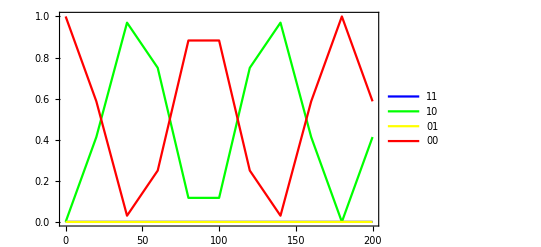

```mathematica
data=Table[{t,Population[DensityMatrix[Evaluate[c[t]/.solution[[1]]]],i,(MaxPhononNumber+1)^2-1]},{i,1,4},{t,0,SimulationTime,SimulationTime/10}];Print[ListLinePlot[data,PlotStyle->({Thick,#}&/@{Blue,Green,Yellow,Red}),PlotLegends->{"11","10","01","00"},Frame->True,PlotRange->All]]
```